```mathematica
itCnt=50;
```

General::munfl: Exp[-1.09089×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7959.84] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

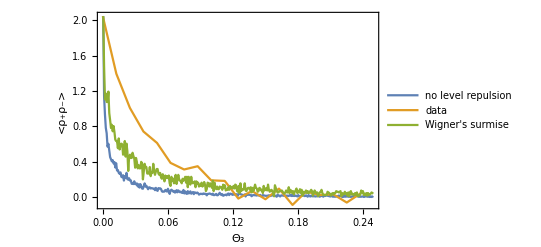

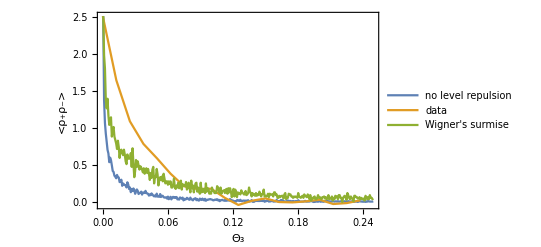

```mathematica
Do[ptsLst=Table[Block[{n=mSize,Ms,As,B,v,c,xs,pts,qs},
Ms=Hermitianize/@(RandomVariate[NormalDistribution[],{3,2,2,2}].{1,ⅈ});
As=RandomVariate[NormalDistribution[],{3,n-2,2,2}].{1,ⅈ};
B=Hermitianize@(RandomVariate[NormalDistribution[],{n-2,n-2,2}].{1,ⅈ});
v=Re@Table[Tr[PauliMatrix[a].M]/2,{a,3},{M,Ms}];
c=Re@Normal@Symmetrize[Table[Tr[PauliMatrix[a].ConjugateTranspose[A1].Inverse[B].A2]/2,{a,3},{A1,As},{A2,As}],Symmetric[{2,3}]];
xs={x1,x2,x3};
pts=xs/.NSolve[v.xs-c.xs.xs,xs,Reals];
pts=Delete[pts,-1];
qs=Sign[(Det[v-2c.#]&/@pts)/Det[v]];
{qs,pts}],itCnt];
ptsSgn=Flatten[Transpose[ptsLst]⟦1⟧];
ptsLoc=Flatten[Transpose[ptsLst]⟦2⟧,1];
ptsFlt=Transpose[{ptsSgn,ptsLoc}];
ptsFltFiltered=GroupBy[ptsFlt,First->Last];
negPtsLst=ptsFltFiltered[-1];
posPtsLst=ptsFltFiltered[1];
binSize=0.005;
posZLst=Abs[posPtsLst⟦All,1⟧];
negZLst=Abs[negPtsLst⟦All,1⟧];
{binPos,histPos}=HistogramList[Abs[posZLst],{binSize}];
{binNeg,histNeg}=HistogramList[Abs[negZLst],{binSize}];
binPosMid=binPos⟦1;;-2⟧+(binPos⟦2⟧-binPos⟦1⟧)/2;
binNegMid=binNeg⟦1;;-2⟧+(binNeg⟦2⟧-binNeg⟦1⟧)/2;
binPos//Length;
fFuncLst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>"ffunc_1d_fitted_dim_3_N_"<>ToString[mSize]<>"_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_n_"<>ToString[Floor[mSize/2-1]]<>"_pol_1_Msh2.npy"]<>")"]];
If[Length[binPos]>Length[binNeg],binZMid=binPosMid,binZMid=binNegMid];
histDiff=Subtract@@PadRight[{histNeg,histPos}];
dataDiff=Transpose@{binZMid,histDiff};
dataNeg=Transpose@{binNegMid,histNeg};
dataNegLog=Transpose@{binNegMid,Log[histNeg]};
dataNegPi=Transpose@{binNegMid/(2π),histNeg};
histNegNorm=histNeg/Total[histNeg⟦1;;628⟧]/2/binSize;
histNegNorm=histNegNorm*fFuncLst⟦1⟧/histNegNorm⟦1⟧;
dataNegPi=Transpose@{binNegMid/(2π),histNegNorm};
(*dataNegPi=dataNegPi*fFuncLst⟦1⟧/dataNegPi⟦1⟧;*)
dataNegNorm=Transpose@{binNegMid,histNeg/Total[histNeg]/2};
dataPos=Transpose@{binPosMid,histPos};
dataPosNorm=Transpose@{binPosMid,histPos/(Total[histPos]/2)};
dataDiffLog=Transpose@{binZMid,Log[histDiff]};
dataNegLog=Transpose@{binNegMid,Log[histNeg]};
ptsLstWig=Table[Block[{n=30,Ms,As,B,v,c,xs,pts,qs,distWig,D},
D=4/(√n);
Ms=Hermitianize/@(RandomVariate[NormalDistribution[],{3,2,2,2}].{1,ⅈ});
As=RandomVariate[NormalDistribution[],{3,1,2,2}].{1,ⅈ};
distWig=ProbabilityDistribution[(1/D)(16/π^2)(En/D)^2 Exp[-4(En/D)^2/π],{En,-∞,∞}];
B=RandomVariate[distWig];
v=Re@Table[Tr[PauliMatrix[a].M]/2,{a,3},{M,Ms}];
c=Re@Normal@Symmetrize[Table[Tr[PauliMatrix[a].ConjugateTranspose[A1].A2/B]/2,{a,3},{A1,As},{A2,As}],Symmetric[{2,3}]];
xs={x1,x2,x3};
pts=xs/.NSolve[v.xs-c.xs.xs,xs,Reals];
pts=Delete[pts,-1];
qs=Sign[(Det[v-2c.#]&/@pts)/Det[v]];
{qs,pts}],itCnt];
ptsLstWig//Length;
ptsSgnWig=Flatten[Transpose[ptsLstWig]⟦1⟧];
ptsLocWig=Flatten[Transpose[ptsLstWig]⟦2⟧,1];
ptsFltWig=Transpose[{ptsSgnWig,ptsLocWig}];
ptsFltFilteredWig=GroupBy[ptsFltWig,First->Last];
negPtsLstWig=ptsFltFilteredWig[-1];
posPtsLstWig=ptsFltFilteredWig[1];
binSizeWig=0.005;
posZLstWig=Abs[posPtsLstWig⟦All,1⟧];
negZLstWig=Abs[negPtsLstWig⟦All,1⟧];
{binPosWig,histPosWig}=HistogramList[Abs[posZLstWig],{binSizeWig}];
{binNegWig,histNegWig}=HistogramList[Abs[negZLstWig],{binSizeWig}];
binPosMidWig=binPosWig⟦1;;-2⟧+(binPosWig⟦2⟧-binPosWig⟦1⟧)/2;
binNegMidWig=binNegWig⟦1;;-2⟧+(binNegWig⟦2⟧-binNegWig⟦1⟧)/2;
binPosWig//Length
If[Length[binPosWig]>Length[binNegWig],binZMidWig=binPosMidWig,binZMidWig=binNegMidWig];
histDiffWig=Subtract@@PadRight[{histNegWig,histPosWig}];
histNegPiWig=histNegWig/Total[histNegWig⟦1;;Floor[π/binSizeWig]⟧]/2/binSizeWig;
histNegPiCompWig=histNegWig/Total[histNegWig⟦1;;Floor[π/binSizeWig]⟧]/2/binSizeWig fFuncLst⟦1⟧/histNegPiWig⟦1⟧;
dataDiffWig=Transpose@{binZMidWig,histDiffWig};
dataNegWig=Transpose@{binNegMidWig,histNegWig};
dataNegLogWig=Transpose@{binNegMidWig,Log[histNegWig]};
dataNegPiWig=Transpose@{binNegMidWig/(2π),histNegWig};
dataNegPiWig=Transpose@{binNegMidWig/(2π),histNegWig/Total[histNegWig⟦1;;Floor[π/binSizeWig]⟧]/2/binSizeWig};
dataNegNormWig=Transpose@{binNegMidWig,histNegWig/Total[histNegWig]/2};
dataPosWig=Transpose@{binPosMidWig,histPosWig};
dataPosNormWig=Transpose@{binPosMidWig,histPosWig/(Total[histPosWig]/2)};
dataDiffLogWig=Transpose@{binZMidWig,Log[histDiffWig]};
dataNegLogWig=Transpose@{binNegMidWig,Log[histNegWig]};
dataNegPiCompWig=Transpose@{binNegMidWig/(2π),histNegPiCompWig};
Print[ListLinePlot[{dataNegPi⟦1;;314⟧,Transpose@{xCoords⟦1;;20⟧,fFuncLst⟦1;;20⟧},dataNegPiCompWig⟦1;;314⟧},PlotRange->All,PlotLabel->M=mSize,PlotLegends->LineLegend[{"no level repulsion","data","Wigner's surmise"}],FrameLabel->{Subscript[Θ, 3],"<ρ_+ρ_->"},Frame->True]]
,{mSize,20,50,10}]
```

```mathematica
"np.load("<>Py[Directory[]<>"\\\\"<>"ffunc_1d_fitted_dim_3_N_"<>ToString[mSize]<>"_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_n_"<>ToString[Floor[mSize/2-1]]<>"_pol_1_Msh2.npy"]<>")"
```

np.load("C:\\Users\\Ohdraw.niL\\Dropbox\\KickedHarperModel\\Note\\Lin\\\\ffunc_1d_fitted_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_n_4_pol_1_Msh2.npy")

```mathematica
mSize=10;
```